```mathematica
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
(* numb of meshes *)
max=5;
```

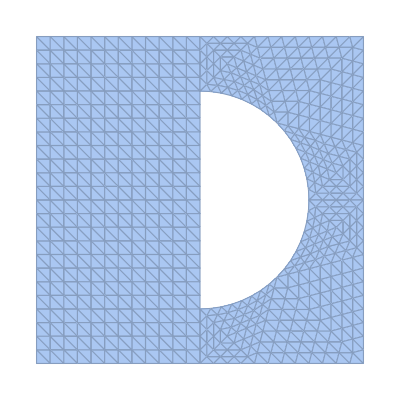

```mathematica
nodes=Import["n.dat","Table"];
triangles=Import["t.dat","Table"]+1;
elements=Triangle/@triangles;
𝒦=MeshRegion[nodes,elements]
HighlightMesh[𝒦,0,MeshCellLabel->{2->"Index"}];
```

```mathematica
u[x_,y_,t_]:=2x y+y^2-t^2 x
Animate[Plot3D[u[x,y,t],{x,y}∈𝒦],{t,0,7},AnimationDirection->ForwardBackward,SaveDefinitions->True,AnimationRunning->False]
```

```mathematica
sphere[θ_,ϕ_]:={Cos[θ] Sin[ϕ/2],Sin[θ] Sin[ϕ/2],Cos[ϕ/2]};
torus[θ_,ϕ_]:={-Sin[ϕ]/3,(2-Cos[ϕ]) Sin[θ]/3,(2-Cos[ϕ]) Cos[θ]/3};
Animate[ParametricPlot3D[(1-λ) sphere[θ,ϕ]+λ torus[θ,ϕ],{θ,0,2 π},{ϕ,0,2 π},PlotRange->1,Mesh->True],{λ,0,1},AnimationDirection->ForwardBackward,SaveDefinitions->True,AnimationRunning->False]
```

```mathematica
Animate[Plot[Sin[x+a],{x,0,10}],{a,0,5},AnimationRunning->False]
```

# Model problems

## Pure Neumann problem on curcular domain

```mathematica
Do[j=ToString[i-1];Subscript[ξ, i]=Import["xi"<>j<>".dat","List"];Subscript[nodes, i]=Import["n"<>j<>".dat","Table"];triangles=Import["t"<>j<>".dat","Table"]+1;elements=Triangle/@triangles;Subscript[𝒦, i]=MeshRegion[Subscript[nodes, i],elements],{i,max}]
```

### Domain

Coarse mesh: h

Numb of nodes: 13

Numb of elements: 16

Nodes’ numeration

-Graphics-

Elements’ numeration

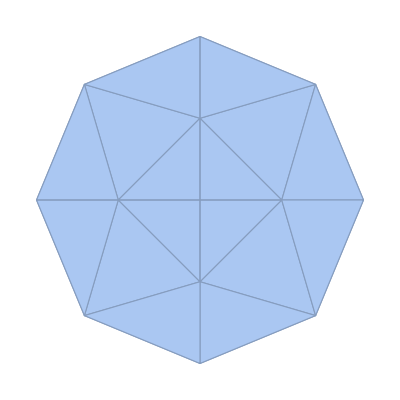

Fine mesh: h / 2

Numb of nodes: 41

Numb of elements: 64

-Graphics-

Fine mesh: h / 3

Numb of nodes: 145

Numb of elements: 256

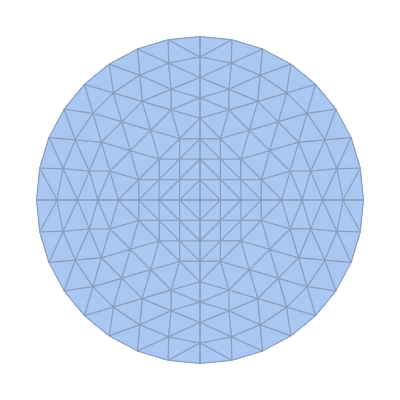

Fine mesh: h / 4

Numb of nodes: 545

Numb of elements: 1024

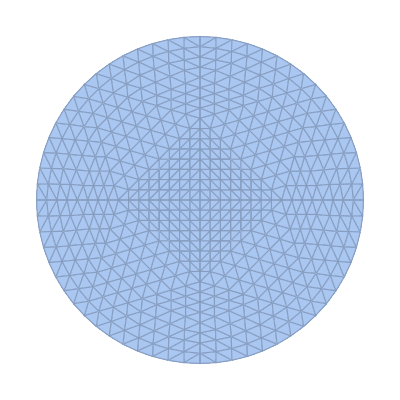

Fine mesh: h / 5

Numb of nodes: 2113

Numb of elements: 4096

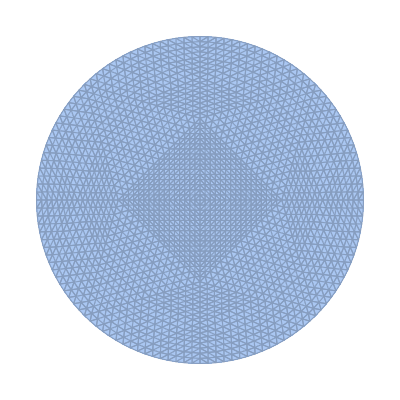

```mathematica
Do[
If[i==1,
Print@Style["Coarse mesh: h","Subsection"],
Print@Style[StringReplace["Fine mesh: h / size","size"-> ToString@i],"Subsection"]
];
Print["Numb of nodes: "<>ToString@MeshCellCount[Subscript[𝒦, i],0]];
Print["Numb of elements: "<>ToString@MeshCellCount[Subscript[𝒦, i],2]];
If[i==1,
Print@Style["Nodes’ numeration",Larger,Bold];
Print@HighlightMesh[Subscript[𝒦, i],0,MeshCellLabel->{0->"Index"}];
Print@Style["Elements’ numeration",Larger,Bold];
Print@HighlightMesh[Subscript[𝒦, i],3,MeshCellLabel->{2->"Index"}],
If[i≥ 3,
Print@Subscript[𝒦, i],
Print@HighlightMesh[Subscript[𝒦, i],0,MeshCellLabel->{0->"Index"}]
]
],
{i,max}]
```

### Plotting

```mathematica
u[x_,y_]:=x^2+y^2+1 
(*u[x_,y_]:=x+2y+3*)
Plot3D[u[x,y],{x,y}∈Subscript[𝒦, max],PlotLabel->"Exact solnn, u(x, y)",AxesLabel->Automatic]
Do[
Subscript[u, h]=Interpolation[Table[{Subscript[nodes, i][[j]],Subscript[ξ, i][[j]]},{j,Length@Subscript[ξ, i]}],InterpolationOrder->1];
Print@Plot3D[Subscript[u, h][x,y],{x,y}∈Subscript[𝒦, i],PlotLabel->StringReplace["FEM soln, u_(h / size)(x,y)","size"-> ToString@i],AxesLabel->Automatic],
{i,max}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

-Graphics3D-

«2 more identical outputs»

### Error analysis

```mathematica
header=Style[#,Bold,Larger]&/@{"i, mesh size := h / i","n := numb of nodes / SLAE size","Δ_i := |u – u_(h / i)|_2","δ_i := Δ_i/(|uSubscriptBox[|, 2])","k := (δ_(i - 1))/δ_i"};
Do[
uVal=Table[u[Subscript[nodes, i][[j,1]],Subscript[nodes, i][[j,2]]],{j,Length@Subscript[ξ, i]}];
Subscript[Δ, i]=Norm[Subscript[ξ, i]-uVal];
Subscript[δ, i]=Subscript[Δ, i]/(Norm@Subscript[ξ, i]);
If[i>1,Subscript[k, i]=Subscript[δ, i-1]/Subscript[δ, i]],
{i,max}]
Subscript[k, 1]="";
data=Table[{i,MeshCellCount[Subscript[𝒦, i],0],ScientificForm[Subscript[Δ, i],3],ScientificForm[Subscript[δ, i],3],NumberForm[Subscript[k, i],3]},{i,max}];
table=Grid[PrependTo[data,header],Frame->All,Spacings-> {1,1}]
```

i, mesh size := h / i | n := numb of nodes / SLAE size | Δ_i := |u – u_(h / i)|_2 | δ_i := Δ_i/(|uSubscriptBox[|, 2]) | k := (δ_(i - 1))/δ_i
1 | 13 | 3.78 | 3.79×10^-1 | 
2 | 41 | 1.57 | 1.31×10^-1 | 2.88
3 | 145 | 7.25×10^-1 | 3.73×10^-2 | 3.53
4 | 545 | 3.49×10^-1 | 9.76×10^-3 | 3.82
5 | 2113 | 1.72×10^-1 | 2.49×10^-3 | 3.93

## (Temp)

Pure Neumann, 
u, c in P_1
a, f in P_2
1) quad basis for a, f
2) quad basis for f
3) linear basis for everything
TODO: test it w/ pure Dirichlet BCs

i, mesh size := h / i | n := numb of nodes / SLAE size | Δ_i := |u – u_(h / i)|_2 | δ_i := Δ_i/(|uSubscriptBox[|, 2]) | k := (δ_(i - 1))/δ_i
1 | 13 | 1.3 | 1.09×10^-1 | 
2 | 41 | 1.56 | 7.65×10^-2 | 1.42
3 | 145 | 9.04×10^-1 | 2.33×10^-2 | 3.28
4 | 545 | 3.3 | 4.43×10^-2 | 0.526
5 | 2113 | 4.77×10^-1 | 3.26×10^-3 | 13.6

i, mesh size := h / i | n := numb of nodes / SLAE size | Δ_i := |u – u_(h / i)|_2 | δ_i := Δ_i/(|uSubscriptBox[|, 2]) | k := (δ_(i - 1))/δ_i
1 | 13 | 3.51 | 2.73×10^-1 | 
2 | 41 | 2.96 | 1.43×10^-1 | 1.91
3 | 145 | 1.06 | 2.74×10^-2 | 5.23
4 | 545 | 6.61 | 8.92×10^-2 | 0.307
5 | 2113 | 7.46×10^-1 | 5.1×10^-3 | 17.5

i, mesh size := h / i | n := numb of nodes / SLAE size | Δ_i := |u – u_(h / i)|_2 | δ_i := Δ_i/(|uSubscriptBox[|, 2]) | k := (δ_(i - 1))/δ_i
1 | 13 | 6.09 | 5.2×10^-1 | 
2 | 41 | 3.4 | 1.6×10^-1 | 3.25
3 | 145 | 7.12×10^-1 | 1.85×10^-2 | 8.65
4 | 545 | 9.84×10^-1 | 1.32×10^-2 | 1.4
5 | 2113 | 1. | 6.85×10^-3 | 1.93